# Mathematica intro (week 1)

# My first notebook

Aly Gillies
23 July 2018

```mathematica
2+3
```

5

## Expressions

```mathematica
5*2-8/2+6^2
1/3 2
1/3*2
1/(3*2)
```

42

2/3

2/3

1/6

## More than a calculator

```mathematica
x=5
?x
```

5

-Graphics-

```mathematica
p=1.5
x=6
3x
x^3.1
x/p
x^(3p)
```

1.5

6

18

258.386

4.

3174.54

-Graphics-

```mathematica
3z
```

3 z

-Graphics-

```mathematica
z=5
```

5

-Graphics-

```mathematica
a=1
b=5
a b
ab
```

1

5

5

ab

## Building functions

```mathematica
f[x_]:=x^2
```

```mathematica
?f
```

-Graphics-

```mathematica
f[4]
f[1.6]
f[Pi]
```

16

2.56

π^2

-Graphics-

```mathematica
u=6;f[u]
```

36

-Graphics-

```mathematica
g[x_]:=f[x]/Sin[x]
```

-Graphics-

```mathematica
f1[x_]:=(x+6)(x+1)
f2[y_]:=(y^3+3)/5
f3[s_]:=s^(1/2)/3
f1[2]
f2[3]
f3[9]
```

24

6

1

## Numerical value - the N function

```mathematica
N[Pi,50]
```

3.1415926535897932384626433832795028841971693993751

## Lists

```mathematica
x1=Range[10]
x2=Table[i,{i,1,11,2}]
```

{1,2,3,4,5,6,7,8,9,10}

{1,3,5,7,9,11}

```mathematica
xido={};Do[AppendTo[xido,i],{i,1,10000,2}];
xiwhile={};i=1;While[i≤10000,AppendTo[xiwhile,i];i=i+2];
For[xifor={};i=1, i≤10000,i=i+2,AppendTo[xifor,i]];
xitable=Table[i,{i,1,10000,2}];
```

```mathematica
xido==xiwhile
xiwhile==xifor
xifor==xitable
```

True

True

True

```mathematica
Timing[xido={};Do[AppendTo[xido,i],{i,1,10000,2}];]
Timing[xiwhile={};i=1;While[i≤10000,AppendTo[xiwhile,i];i=i+2];]
Timing[For[xifor={};i=1, i≤10000,i=i+2,AppendTo[xifor,i]];]
Timing[xitable=Table[i,{i,1,10000,2}];]
```

{0.087538,Null}

{0.095849,Null}

{0.092215,Null}

{0.000338,Null}

```mathematica
(*more than simple expression in Table's first argument*)
myList=Table[{i,i^2},{i,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
TableForm[myList]
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100

```mathematica
myList//TableForm
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100

-Graphics-

```mathematica
Range[1,11,2]
```

{1,3,5,7,9,11}

-Graphics-

```mathematica
Table[Prime[i],{i,1,10}]
```

{2,3,5,7,11,13,17,19,23,29}

-Graphics-

```mathematica
invest[n_]:=1000*1.05^n
years=Range[5]
```

{1,2,3,4,5}

-Graphics-

```mathematica
years//invest
```

{1050.,1102.5,1157.63,1215.51,1276.28}

-Graphics-

```mathematica
mySines=Table[{θ,Sin[θ]},{θ,0,2π,π/4}]
```

{{0,0},{π/4,1/(√2)},{π/2,1},{(3 π)/4,1/(√2)},{π,0},{(5 π)/4,-1/(√2)},{(3 π)/2,-1},{(7 π)/4,-1/(√2)},{2 π,0}}

-Graphics-

```mathematica
N[mySines]
```

{{0.,0.},{0.785398,0.707107},{1.5708,1.},{2.35619,0.707107},{3.14159,0.},{3.92699,-0.707107},{4.71239,-1.},{5.49779,-0.707107},{6.28319,0.}}

## List manipulation

```mathematica
myList=Table[Fibonacci[n],{n,1,50}]
myList[[10]]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578,5702887,9227465,14930352,24157817,39088169,63245986,102334155,165580141,267914296,433494437,701408733,1134903170,1836311903,2971215073,4807526976,7778742049,12586269025}

55

```mathematica
Fibonacci[10]
```

55

```mathematica
Length[myList]
Dimensions[myList]
```

50

{50}

```mathematica
Select[myList,PrimeQ]
```

{2,3,5,13,89,233,1597,28657,514229,433494437,2971215073}

-Graphics-

```mathematica
a=Range[5]
b=Table[i^2,{i,1,5}]
```

{1,2,3,4,5}

{1,4,9,16,25}

-Graphics-

```mathematica
Join[a,b]
Union[a,b]
Intersection[a,b]
```

{1,2,3,4,5,1,4,9,16,25}

{1,2,3,4,5,9,16,25}

{1,4}

-Graphics-

```mathematica
c={a,6,7}
d={b, 36,49}
```

{{1,2,3,4,5},6,7}

{{1,4,9,16,25},36,49}

```mathematica
e=Flatten[c]
f=Flatten[d]
```

{1,2,3,4,5,6,7}

{1,4,9,16,25,36,49}

```mathematica
g={e,f}
```

{{1,2,3,4,5,6,7},{1,4,9,16,25,36,49}}

-Graphics-

```mathematica
Transpose[g]
Transpose[g]//TableForm
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49}}

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49

## Plotting graphs

### Plotting using a function

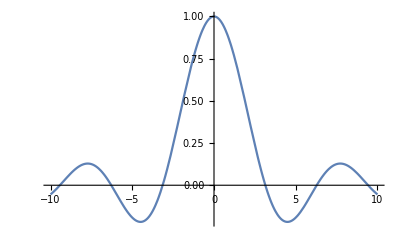

```mathematica
Plot[Sinc[x],{x,-10,10}]
```

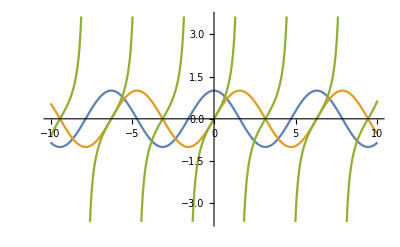

```mathematica
Plot[{Cos[x],Sin[x],Tan[x]},{x,-10,10}]
```

### Options

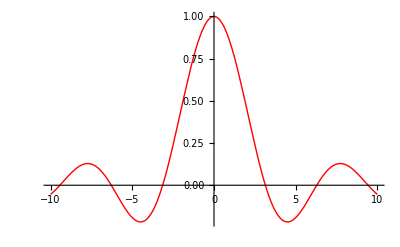

```mathematica
Plot[Sinc[x],{x,-10,10}, PlotStyle->{Red,Thick}]
```

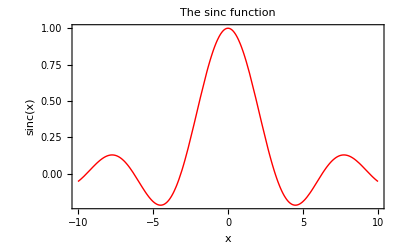

```mathematica
Plot[Sinc[x],{x,-10,10}, PlotStyle->{Red,Thick}, PlotLabel->"The sinc function", Frame->True, FrameLabel->{x,Sinc[x]}]
```

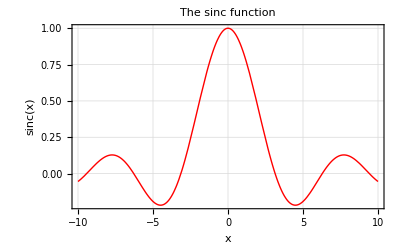

```mathematica
Plot[Sinc[x],{x,-10,10}, PlotStyle->{Red,Thick}, PlotLabel->"The sinc function", Frame->True, FrameLabel->{x,Sinc[x]},GridLines->Automatic]
```

-Graphics-

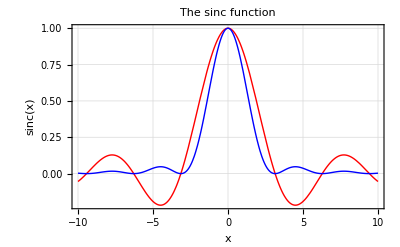

```mathematica
Plot[{Sinc[x],Sinc[x]^2},{x,-10,10}, PlotStyle->{{Red,Thick},{Blue,Thick}}, PlotLabel->"The sinc function", Frame->True, FrameLabel->{x,Sinc[x]},GridLines->Automatic]
```

-Graphics-

```mathematica
Plot[Tooltip[{Sinc[x],Sinc[x]^2}],{x,-10,10}, PlotStyle->{{Red,Thick},{Blue,Thick}}, PlotLabel->"The sinc function", Frame->True, FrameLabel->{x,Sinc[x]},GridLines->Automatic]
```

-Graphics-

-Graphics-

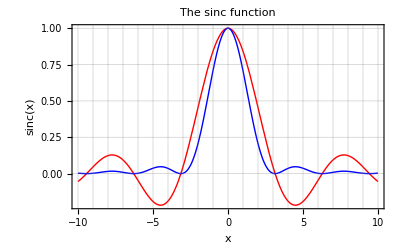

```mathematica
Plot[{Sinc[x],Sinc[x]^2},{x,-10,10}, PlotStyle->{{Red,Thick},{Blue,Thick}}, PlotLabel->"The sinc function", Frame->True, FrameLabel->{x,Sinc[x]},GridLines->{Range[-10,10],Range[-0.25,1,0.25]}]
```

-Graphics-

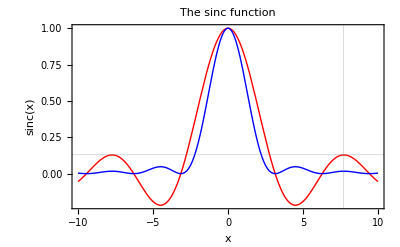

```mathematica
Plot[{Sinc[x],Sinc[x]^2},{x,-10,10}, PlotStyle->{{Red,Thick},{Blue,Thick}}, PlotLabel->"The sinc function", Frame->True, FrameLabel->{x,Sinc[x]},GridLines->{{7.7},{0.13}}]
```

### Plotting using a list

{0.0000509881,0.000132513,0.000356011,0.000755024,0.0014775,0.00399599,0.00773905,0.0168426,0.0257412,0.041548,0.0957856,0.153048,0.237643,0.244436,0.434369,0.439808,0.788899,0.701724,1.00799,0.86575,0.977519,1.07525,0.807456,0.65001,0.595398,0.472025,0.347608,0.246297,0.201764,0.152045,0.0656933,0.0494557,0.0320909,0.0141329,0.00605017,0.00339399,0.00181285,0.000731052,0.000304711,0.000139832,0.0000485338}

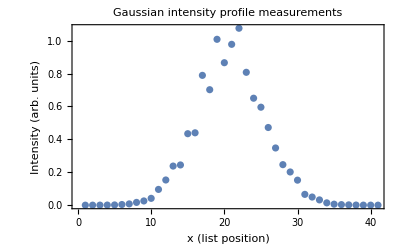

```mathematica
myProfile=Table[RandomReal[{0.8,1.2}]Exp[-0.1x^2],{x,-10,10,0.5}]
ListPlot[myProfile,Frame->True,
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (list position)","Intensity (arb. units)"}]
```

-Graphics-

{{-10.,0.0000398798},{-9.5,0.000125136},{-9.,0.000247922},{-8.5,0.00061714},{-8.,0.00164297},{-7.5,0.00384667},{-7.,0.00611453},{-6.5,0.0162976},{-6.,0.0283472},{-5.5,0.0511385},{-5.,0.0744482},{-4.5,0.134456},{-4.,0.23331},{-3.5,0.278717},{-3.,0.447264},{-2.5,0.620782},{-2.,0.65581},{-1.5,0.764789},{-1.,1.04528},{-0.5,1.1148},{0.,0.845968},{0.5,0.909611},{1.,0.935704},{1.5,0.827593},{2.,0.558689},{2.5,0.438868},{3.,0.486149},{3.5,0.309108},{4.,0.205408},{4.5,0.142306},{5.,0.0865498},{5.5,0.0452476},{6.,0.0252636},{6.5,0.0164467},{7.,0.00871763},{7.5,0.00292796},{8.,0.00145164},{8.5,0.000802277},{9.,0.00025574},{9.5,0.000127673},{10.,0.0000405978}}

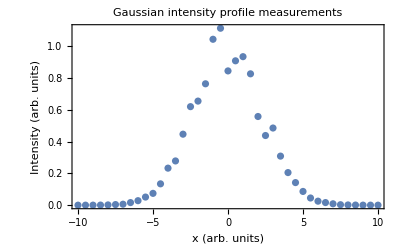

```mathematica
myProfile=Table[{x,RandomReal[{0.8,1.2}]Exp[-0.1x^2]},{x,-10,10,0.5}]
ListPlot[myProfile,Frame->True,
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
```

-Graphics-

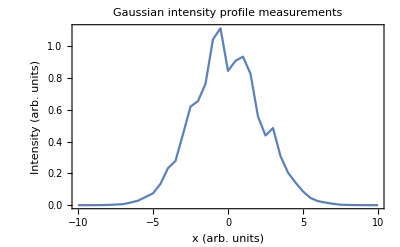

```mathematica
ListPlot[myProfile,Frame->True,
PlotLabel->"Gaussian intensity profile measurements",FrameLabel->{"x (arb. units)","Intensity (arb. units)"}, Joined->True]
```

-Graphics-

```mathematica
ListLinePlot[myProfile,Frame->True,
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
```

-Graphics-

-Graphics-

```mathematica
a=.;b=.;x=.
FindFit[myProfile,a Exp[-b x^2],{a,b},x]
```

{a→0.997573,b→0.0972193}

## Rules

```mathematica
model = a Exp[-b x^2];sol=FindFit[myProfile, model, {a,b},x]
myFit[x_]:=model/.sol
```

{a→0.997573,b→0.0972193}

-Graphics-

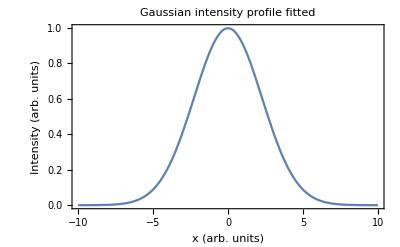

```mathematica
Plot[myFit[x],{x,-10,10}, Frame->True, 
PlotLabel->"Gaussian intensity profile fitted",FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
```

-Graphics-

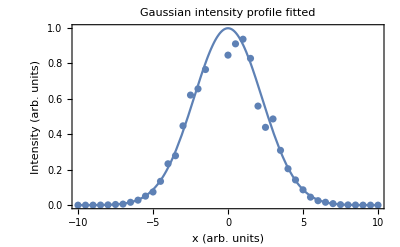

```mathematica
Show[Plot[myFit[x],{x,-10,10}, Frame->True, 
PlotLabel->"Gaussian intensity profile fitted",FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
,ListPlot[myProfile,Frame->True,
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]]
```

-Graphics-

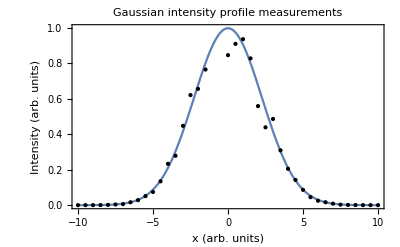

```mathematica
Plot[myFit[x],{x,-10,10}, Frame->True,Epilog->{Point[myProfile]},
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
```

-Graphics-

General::munfl: Exp[-972.114] is too small to represent as a normalized machine number; precision may be lost.

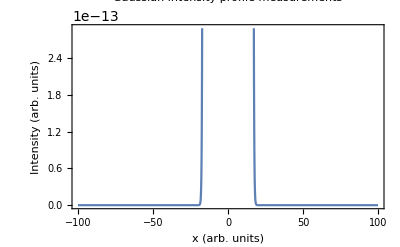

```mathematica
On[General::munfl] (* make sure the underflow warning is active initially *)
Plot[myFit[x],{x,-100,100}, Frame->True,Epilog->{Point[myProfile]},
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
```

```mathematica
Off[General::munfl] (* tell Mathematica not to warn about underflow *)
Plot[myFit[x],{x,-100,100}, Frame->True,Epilog->{Point[myProfile]},
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
```

-Graphics-

-Graphics-

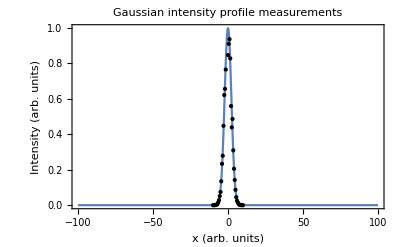

```mathematica
Plot[myFit[x],{x,-100,100}, Frame->True,Epilog->{Point[myProfile]}, PlotRange->All,
PlotLabel->"Gaussian intensity profile measurements", FrameLabel->{"x (arb. units)","Intensity (arb. units)"}]
```

## Manipulate and animate

```mathematica
Manipulate[Plot[Sin[5t-ϕ],{t,0,2π}, AxesLabel->{"t","Sin[5t-ϕ]"}],{ϕ,0,2π}]
```

-Graphics-

```mathematica
Manipulate[Plot[Sin[ω t-ϕ],{t,0,2π}],{ϕ,0,2π},{{ω,5},1,10}]
```

## Scope of variables

```mathematica
sincurve=Sin[5t-ϕ];
Manipulate[Plot[sincurve,{t,0,2π}],{ϕ,0,2π}]
```

```mathematica
sincurve=. (*unset the old definition ot prevent an "is Protected" error*)
sincurve[ϕ_]=Sin[5t-ϕ];
Manipulate[Plot[sincurve[ϕ],{t,0,2π}],{ϕ,0,2π}]
```

## 3D plotting

```mathematica
Plot3D[Sin[x]Cos[y],{x,-2π,2π},{y,-2π,2π}, PlotStyle->{Opacity[0.8]},
AxesLabel->{"x","y"}, PlotLabel->"Egg box function"]
```

-Graphics3D-

-Graphics-

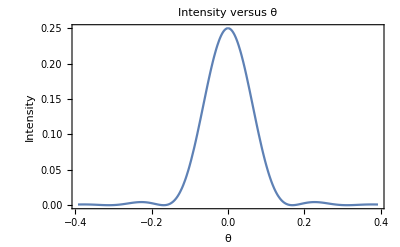

```mathematica
λ=550.*10^-9; (*m*)
k=2π/λ;
a=2*10^-6;(*m*)
int[θ_]:=(BesselJ[1, k a Sin[θ]]/(k a Sin[θ]))^2
Plot[int[θ],{θ,-π/8,π/8},PlotRange->All,Frame->True,PlotLabel->"Intensity versus θ",FrameLabel->{"θ","Intensity"}]
```

-Graphics-

```mathematica
θ[x_]:=ArcSin[x/Sqrt[x^2+R^2]]
```

-Graphics-

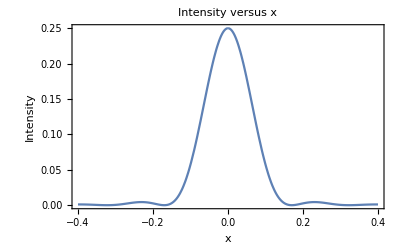

```mathematica
R=1; (*m*)
int[x_]:=(BesselJ[1,k a Sin[θ[x]]]/(k a Sin[θ[x]]))^2;
Plot[int[x],{x,-0.4,0.4},PlotRange->All,Frame->True,PlotLabel->"Intensity versus x",FrameLabel->{"x","Intensity"}]
```

-Graphics-

```mathematica
min=FindMinimum[int[x],{x,0.16}]
```

{9.39547×10^-18,{x→0.170114}}

-Graphics-

```mathematica
θ[x_,y_]:=ArcSin[Sqrt[x^2+y^2]/Sqrt[x^2+y^2+R^2]]
```

-Graphics-

```mathematica
int3d[x_,y_]:=(BesselJ[1,k a Sin[θ[x,y]]]/(k a Sin[θ[x,y]]))^2;
Plot3D[int3d[x,y],{x,-0.4,0.4},{y,-0.4,0.4},PlotRange->All,PlotLabel->"Intensity versus (x,y)",AxesLabel->{"x","y","Intensity"}]
```

-Graphics3D-

-Graphics-

```mathematica
Plot3D[int3d[x,y],{x,-0.4,0.4},{y,-0.4,0.4},PlotRange->All,PlotLabel->"Intensity versus (x,y)",AxesLabel->{"x","y","Intensity"},ColorFunction->Hue,PlotStyle->{Opacity[0.4]},Mesh->50]
```

-Graphics3D-

-Graphics-

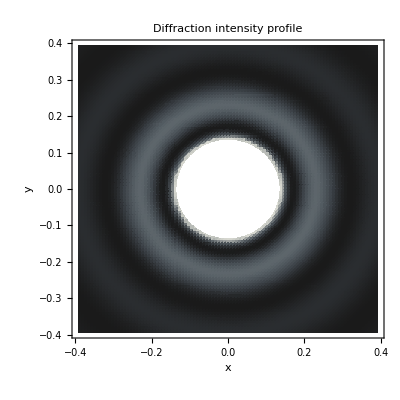

```mathematica
DensityPlot[int3d[x,y],{x,-π/8,π/8},{y,-π/8,π/8},PlotPoints->100,PlotRange->{0,0.01}, ColorFunction->"GrayTones",
PlotLabel->"Diffraction intensity profile", FrameLabel->{"x","y"}]
```